```mathematica
PrependTo[$Path,"/Users/annils14/Documents/KerrModes"];
Needs["KerrTTML`"]
SetSpinWeight[-2]
SelectMode[PolynomialMode]
```

All KerrMode routines (TTML) set for Spin-Weight s = -2

Mode set to find Polynomial solutions

```mathematica
SchTTMLTable[2]=2;
SchTTMLTable[2,0]={0.001-2.001*I,0,0,0,0};
SchTTMLTable[2,1]={0.35-0.27*I,0,0,0,0};
SchTTMLTable[3]=2;
SchTTMLTable[3,0]={0.6-0.09*I,0,0,0,0};
SchTTMLTable[3,1]={0.6-0.28*I,0,0,0,0};
```

```mathematica
SchTTMLTable[2,0]
```

{0.-2. ⅈ,0,0,0,0}

```mathematica
SchwarzschildTTML[2,0,RadialDebug->1,SchDebug->0]
```

Computing (l=2,n=0)

δω=-0.000999500249999850200753259+0.000999999750249789883540794 ⅈ  root=0.814790684129320946548078

δω=-0.000293026998100418974970208+0.000292716642161629024499628 ⅈ  root=0.23860453352994433170791

δω=-4.288693947742206947529×10^-8-4.54463368441212505051966×10^-11 ⅈ  root=0.0000247028910080702197045188

KerrModes`Private`RadialLentzStep::pflag: Set $MinPrecision =32

δω=9.7452714890090918815619276061311×10^-19-4.5982187813861510023011623265972×10^-16 ⅈ  root=2.6485799663426761104701342344683×10^-13

KerrModes`Private`RadialLentzStep::pflag: Set $MinPrecision =48

δω=-2.24054451963581808753211165981620722065411131357×10^-34+5.28588024779398388053929234951524909564301604718×10^-32 ⅈ  root=3.04469437418045907328422309495722749033891767611×10^-29

SetPrecision::precsm: Requested precision 24 is smaller than $MinPrecision. Using $MinPrecision instead.

KerrModes`Private`RadialLentzStep::increase: Excessive increase in Precision, Abort

$Aborted

```mathematica
\
```

```mathematica
$MinPrecision=24
```

24

```mathematica
Plot3D[Abs[PlotContFrac[0,-2,-1,1/2,4,ωr-ⅈ ωi,300,15]],{ωr,0,10},{ωi,0,10}]
```

-Graphics3D-

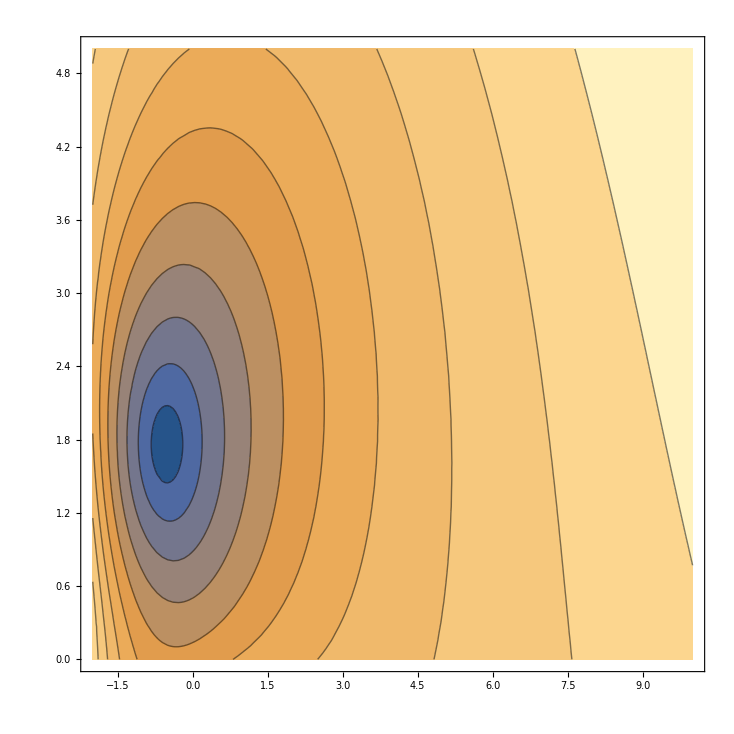

```mathematica
ContourPlot[Abs[PlotContFrac2[0,-2,-2,1/8,1,ωr-ⅈ ωi,300,15]],{ωr,-2,10},{ωi,0,5},Contours->10]
```

```mathematica
Plot3D[{Re[PlotContFrac2[0,-2,-1,1/2,1,ωr-ⅈ ωi,3000,15]],Im[PlotContFrac2[0,-2,-1,1/2,1,ωr-ⅈ ωi,3000,15]]},{ωr,0,5},{ωi,0,5}]
```

-Graphics3D-

```mathematica
Plot3D[{Re[RadialCFRem[0,-2,0,0,4,ωr-ⅈ ωi,300][[1]]],Im[RadialCFRem[0,-2,0,0,4,ωr-ⅈ ωi,300][[1]]]},{ωr,0,4},{ωi,0,4}]
```

-Graphics3D-

```mathematica
RadialCFRem[0,-2,0,0,10,-ⅈ 10,2]
```

RadialCFRem[0,-2,0,0,10,-10 ⅈ,2]

```mathematica
SchwarzschildTTML[2,0,RadialDebug->1,SchDebug->0]
```

Computing (l=2,n=0)

Have made it into RadialCFRem

Have made it into RadialCFRem

Have made it into RadialCFRem

«17 more identical outputs»

KerrModes`Private`RadialLentzStep::increase: Excessive increase in Precision, Abort

$Aborted

```mathematica
?SchwarzschildTTML
```

SchwarzschildTTML[l,n] computes the Quasi-Normal Mode solutions for overtone n of mode l.  The mode is computed to an accuracy of 10^-14.  For given 'l', if solutions with overtones (n-1) and (n-2) have not been computed, then the routine is recersively called for overtone '(n-1).  If no solutions exist for mode l, then the first two overtones of (l-1) and (l-2) are used to extrapolate initial guesses for these modes.

Options:
	 SpinWeight→Null : -2,-1,0
		 The spin weight must be set via a call to SetSpinWeight before any KerrTTML
		 function call.
	 ModePrecision→24
	 JacobianStep→-10
		 The radial solver make use of numerical derivatives.  The relative step size
		 is set to 10^JacobianStep.
	 RadialCFMinDepth→300
		 The minimum value for the Radial Continued Fraction Depth.
	 RadialCFDepth→1
		 The initial Radial Continued Fraction Depth is usually taken from the prior 
		 solution in the sequence.  Fractional values reduce this initial value by that
		 fraction.  Integer values larger than RadialCFMinDepth are used as the new
		  initial value.
	 RadialRelax→1
		 Initial under-relaxation parameter used in Radial Newton iterations.
	 Rootϵ→-14
		 10^Rootϵ is the maximum allowed magnitude for the Radial Continued Fraction.
	 SchDebug→0 : 0,1,2,3,...
		 'Verbosity' level during the Schwarzschile iterations.
	 RadialDebug→0 : 0,1,2,3,...
		 'Verbosity' level during the Radial Newton iterations.